# Learning tabular data

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

## Get data

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],
"PurchasePrice"->encoders["PurchasePrice"],
"MaintenanceCost"->encoders["MaintenanceCost"],
"Doors"->encoders["Doors"],
"Passengers"->encoders["Passengers"],
"Cargo"->encoders["Cargo"],
"Safety"->encoders["Safety"]
];
```

## Create net

```mathematica
{softNet,hardNet}=Block[{numClasses=Length[classes],classificationLayerSize},
classificationLayerSize=180*numClasses;
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
BatchSize->Automatic,
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
trainedSoftNet=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[result["TrainedNet"]],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
];
```

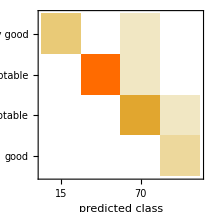
Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.10.5) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.962 ± 0.0065
Mean cross entropy | 0.0386 ± 0.0067
Single evaluation time | 4.32 ms/example
Batch evaluation speed | 2.24 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet,testData->"Acceptability"]
```

```mathematica
trainedSoftNet2=HardNetTransformWeights[trainedSoftNet,(If[#>0.5,1,0]&)/@#&]
```

NetGraph[<>]

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet2,testData->"Acceptability"]
```

Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.10.5) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.962 ± 0.0065
Mean cross entropy | 0.0386 ± 0.0067
Single evaluation time | 2.76 ms/example
Batch evaluation speed | 1.13 examples/ms
-Graphics- |

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
```

```mathematica
hncwt=HardNetClassify[hnf,featureLayer,NetDecoder[encoders["Acceptability"]],testData,"Acceptability"];
eval=HardNetClassifyEvaluation[hncwt]
```

<|Accuracy→0.988439,Counts→<|<|Prediction→unacceptable,Target→unacceptable|>→250,<|Prediction→acceptable,Target→acceptable|>→68,<|Prediction→very good,Target→very good|>→14,<|Prediction→good,Target→good|>→10,<|Prediction→acceptable,Target→unacceptable|>→1,<|Prediction→acceptable,Target→very good|>→1,<|Prediction→good,Target→acceptable|>→1,<|Prediction→good,Target→very good|>→1|>|>

```mathematica
tmp1=Map[
With[{d=Drop[#,-1]},
{Flatten[Values[trainedSoftNet[d,"Probabilities"]]],Flatten[HardNetClassProbabilities[HardNetClassScores[HardNetClassBits[hnf,featureLayer,{d}]]]]}
]&,Normal[testData]];
```

$Aborted

```mathematica
With[{d=#},Total[d[[1]]-d[[2]]]<0.00001]&/@tmp1
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
softWeights=Flatten[ExtractWeights[trainedSoftNet]];
```

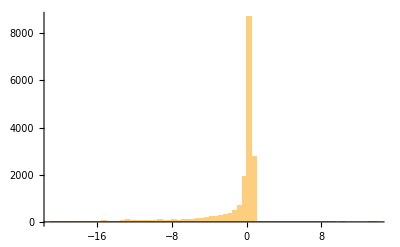

```mathematica
Histogram[softWeights,PlotRange->All]
```